## Model Summary

```mathematica
countparameters[l_ConvolutionLayer|l_LinearLayer|l_ConstantArrayLayer|l_EmbeddingLayer|l_BatchNormalizationLayer|l_BasicRecurrentLayer|l_GatedRecurrentLayer|l_LongShortTermMemoryLayer]:=<|NetExtract[l,"Type"]->(NetExtract[NetInitialize@l,"Arrays"]//Query[Select[ArrayQ]]//Map[Length@*Flatten])|>

countparameters[l_SpatialTransformationLayer]:=<|NetExtract[l,"Type"]-><|"Parameters"->6|>|>

countparameters[l_NetChain|l_NetGraph]:=l//Normal//Map[countparameters]
(*other layers assumed to be non-learnable *)
countparameters[_]:=Nothing
```

```mathematica
summary[net_NetGraph]:=Module[{sum,parameterCounts},
sum[x_Integer]:=x;
sum[x:<|(_->_Integer)..|>]:=Total@Values@x;
sum[x_List]:=x//Total;
sum[_]:=0;

parameterCounts=net//countparameters;
<|"Total"->(parameterCounts//Map[sum,#,{0,Infinity}]&),"Details"->(parameterCounts//Map[sum,#,{1,Infinity}]&)|>]
```

## Model Info

```mathematica
inModelDir=FileNameJoin[{NotebookDirectory[],"PretrainedModels","ImageNet"}];
inModels=FileNames["*.WLNet",inModelDir];
inModelInfo=Flatten[
StringCases[inModels,"ImageNet\\"~~m___~~" Trained on "~~ds___~~".WLNet":>{m,ds}],
{2}][[1]]/."ImageNet Competition Data"->"ImageNet";
inModelMtrx=inModelInfoᵀ~Append~inModelsᵀ;
```

```mathematica
Exit[]
```

```mathematica
nParamAssoc=AssociationThread[inModelInfo->(Boole@StringFreeQ[ToString@Information[Import[#],"Layers"],"BatchNormalizationLayer"]&/@mdlFnames)];
```

{False}

```mathematica
mdlFnames=Last/@inModelMtrx;
nParamAssoc=AssociationThread[inModelInfo->(Information[
NetChain[{
NetTake[#,{1,-3}],
NetChain[{LinearLayer[2],SoftmaxLayer[]}]
}]&@Import[#],
"ArraysTotalElementCount"
]&/@mdlFnames)];
```

```mathematica
mdlFnames=Last/@inModelMtrx;
nParamAssoc=AssociationThread[inModelInfo->(Information[Import[#],"ArraysTotalElementCount"]&/@mdlFnames)];
```

```mathematica
activations=NetMeasurements[NetFlatten@Import[Last@mdlFnames],testData,NetPort[{1,"Output"}]];
ArrayPlot[ArrayFlatten@Partition[activations,5],ColorFunction->"Rainbow",FrameTicks->None]
```

NetMeasurements::invtdata: Training data should be an association of lists, or a rule from input to output examples.

Partition::pdep: Depth 1 requested in object with dimensions {}.

ArrayFlatten::depth: The ArrayDepth of the expression at position 1 of ArrayFlatten[Partition[$Failed,5]] must be at least equal to the specified rank 2. (The rank is given by the optional second argument, which defaults to 2.)

ArrayPlot::mat: Argument ArrayFlatten[Partition[$Failed,5]] at position 1 is not a list of lists.

ArrayPlot[ArrayFlatten[Partition[$Failed,5]],ColorFunction→Rainbow,FrameTicks→None]

```mathematica
inModelInfo
```

{{Ademxapp Model A,ImageNet},{EfficientNet,ImageNet with AdvProp and AutoAugment},{EfficientNet,ImageNet with NoisyStudent},{EfficientNet,ImageNet},{Inception V1,ImageNet},{Inception V3,ImageNet},{MobileNet V2,ImageNet},{ResNet-101,ImageNet},{ResNet-152,ImageNet},{ResNet-50,ImageNet},{Squeeze-and-Excitation Net,ImageNet},{SqueezeNet V1.1,ImageNet},{VGG-16,ImageNet},{VGG-19,ImageNet},{Wide ResNet-50-2,ImageNet}}

```mathematica
colors={{RGBColor[0.28240003484173815, 0.6090799721266095, 0.7538800418100857],RGBColor[0.337228, 0.447663, 1.],RGBColor[0.519913, 0.338384, 0.950217],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.68343, 0.28, 0.602415]},{RGBColor[0.560181, 0.691569, 0.194885]},{RGBColor[1., 0.4175572158598194, 0.6625177087370098]},{RGBColor[0.969644, 0.598219, 0.081962],RGBColor[1, 0.75, 0]},{Hue[0, 0.7, 0.9],Hue[0.01, 0.8, 0.8]},{GrayLevel[0],GrayLevel[0.5]}};
```

## Score Scatter v2

```mathematica
ColorData[97]/@Range[5]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351]}

```mathematica
resultsDir=FileNameJoin[{NotebookDirectory[],"FinalResults\\NoInternalUpdatingModelComparison"}];
fnames=FileNames["*mx",resultsDir];
```

```mathematica
groupedNets={{"SqueezeNet V1.1","EfficientNet","MobileNet V2"},{"Ademxapp Model A","ResNet-101","ResNet-152","ResNet-50","Wide ResNet-50-2"},{"Inception V1","Inception V3"},{"Squeeze-and-Excitation Net"},{"VGG-16","VGG-19"}};
groupedNets=Map[{#,"ImageNet"}&,groupedNets,{-1}];

netTypes={"Minimal Architectures","Residual Networks","GoogLeNets","SENets","VGGs"};

pointShapes={"■","□","●","○","◆","◇","★","☆"};
pointShapes={"■","●","◆","▲","★"};
pointShapes=pointShapes[[;;Length@groupedNets]];

colors={{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885]},{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351]},{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051]},{RGBColor[0.368417, 0.506779, 0.709798]},{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051]}};

fnames5Class=Rest@Select[fnames,StringContainsQ["5Class"]];
netkeys=Flatten[
StringCases[fnames5Class,"Class - "~~m___~~" - "~~ds___~~"Pretrain.mx":>{m,ds}],
{2}][[1]]/."ImageNet Competition Data"->"ImageNet";
accuracies5Class=Table[
results=AssociationTranspose@Import[fname];
Around[Median[#],{Median[#]-Min[#],Max[#]-Median[#]}]&@(Max/@(#["Accuracy"]&/@results["ValidationMeasurementsLists"]))
,{fname,fnames2Class}];
accuracies5ClassAssoc=AssociationThread[netkeys->accuracies5Class];
Show[ListPlot[
List/@KeyValueMap[{nParamAssoc[#1],#2}&,KeyTake[accuracies5ClassAssoc,#1]],
PlotStyle->#3,PlotMarkers->Style[#4,16],
ScalingFunctions->{"Log",None},GridLines->{Full,Automatic},GridLinesStyle->Lighter@LightGray
]&@@@({groupedNets,netTypes,colors,pointShapes}ᵀ),
ScalingFunctions->"Log",PlotRange->{Automatic,{0.96,1}},
Frame->True,FrameLabel->{{"Accuracy",None},{"Internal Parameters","2-Class Problem"}},
Axes->False]
```

Select::normal: Nonatomic expression expected at position 1 in Select[fnames,StringContainsQ[5Class]].

StringCases::strse: String or list of strings expected at position 1 in StringCases[Select[StringContainsQ[5Class]],Class - ~~m___~~ - ~~ds___~~Pretrain.mx:>{m,ds}].

Flatten::fldep: Level 2 specified in {{2}} exceeds the levels, 1, which can be flattened together in StringCases[Select[StringContainsQ[5Class]],Class - ~~m___~~ - ~~ds___~~Pretrain.mx:>{m,ds}].

Table::iterb: Iterator {fname,fnames2Class} does not have appropriate bounds.

-Graphics-

```mathematica
abrvAssoc=<|"Ademxapp Model A"->"AM A?","RandomForestClassifier"->"RFC","EfficientNet"->"EN","MLPClassifier"->"MLP","Inception V1"->"IN V1","Inception V3"->"IN V3","GradientBoostingClassifier"->"GB","ResNet-50"->"RN-50","Wide ResNet-50-2"->"wRN-50-2","ResNet-101"->"RN-101","ResNet-152"->"RN-152","Squeeze-and-Excitation Net"->"SEN","SqueezeNet V1.1"->"SN","VGG-16"->"VGG-16","VGG-19"->"VGG-19","Hadamard"->"H","LatentSemanticAnalysis"->"LSA","LLE"->"LLE","VotingClassifier"->"VC","MultidimensionalScaling"->"MS","PrincipalComponentsAnalysis"->"PCA","TSNE"->"TSNE","LinearSVC"->"lSVC","KNeighborsClassifier"->"KNN","AdaBoostClassifier"->"AB","GaussianNB"->"gNB","MobileNet V2"->"MN V2"|>;
```

```mathematica
Grid[{{Style["Architecture",Bold,Underlined],}}~Join~((Sequence@@(({(Function[{clr},Style[#4,clr,Bold]]/@#3),abrvAssoc[#1]&/@#1⟦;;,1⟧}ᵀ)~Prepend~{Style[#2,Bold(*,Underlined*)],})&)@@@({groupedNets,netTypes,colors,pointShapes}ᵀ)),Alignment->Left]
```

Architecture | 
Minimal | 
■ | EN
■ | MN V2
■ | SN
Residual | 
● | RN-101
● | RN-152
● | RN-50
● | wRN-50-2
GoogLeNet | 
◆ | IN V1
◆ | IN V3
SENet | 
▲ | SEN
VGG | 
▼ | VGG-16
▼ | VGG-19

```mathematica
Select[fnames5Class,StringContainsQ["EfficientNet"]]
```

{}

```mathematica
netkeys
```

{{Inception V1,ImageNet},{Inception V3,ImageNet},{MobileNet V2,ImageNet},{ResNet-101,ImageNet},{ResNet-152,ImageNet},{ResNet-50,ImageNet},{Squeeze-and-Excitation Net,ImageNet},{SqueezeNet V1.1,ImageNet},{VGG-16,ImageNet},{VGG-19,ImageNet},{Wide ResNet-50-2,ImageNet}}

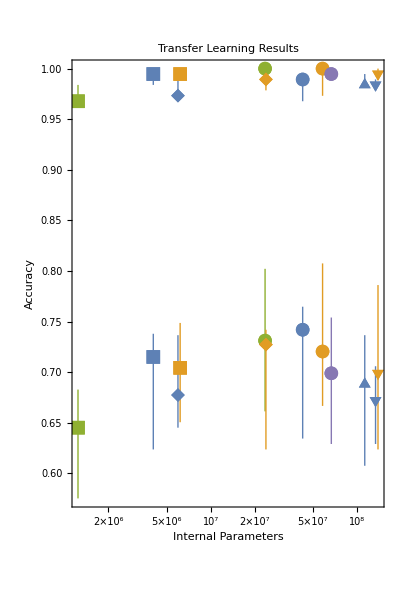

```mathematica
resultsDir=FileNameJoin[{NotebookDirectory[],"FinalResults\\NoInternalUpdatingModelComparison"}];
fnames=FileNames["*mx",resultsDir];

groupedNets={{"SqueezeNet V1.1","EfficientNet","MobileNet V2"},{(*"Ademxapp Model A",*)"ResNet-101","ResNet-152","ResNet-50","Wide ResNet-50-2"},{"Inception V1","Inception V3"},{"Squeeze-and-Excitation Net"},{"VGG-16","VGG-19"}};
groupedNets=Sort/@groupedNets;
groupedNets=Map[{#,"ImageNet"}&,groupedNets,{-1}];

netTypes={"Minimal","Residual","GoogLeNet","SENet","VGG"};

pointShapes={"■","●","◆","▲","▼"};
pointShapes=pointShapes[[;;Length@groupedNets]];

colors={{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885]},{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.528488, 0.470624, 0.701351]},{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051]},{RGBColor[0.368417, 0.506779, 0.709798]},{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051]}};

fnames5Class=Select[fnames,StringContainsQ["5Class"]];
netkeys=Flatten[
StringCases[fnames5Class,"Class - "~~m___~~" - "~~ds___~~"Pretrain.mx":>{m,ds}],
{2}][[1]]/."ImageNet Competition Data"->"ImageNet";
accuracies5Class=Table[
results=AssociationTranspose@Import[fname];
Around[Median[#],{Median[#]-Min[#],Max[#]-Median[#]}]&@(Max/@(#["Accuracy"]&/@results["ValidationMeasurementsLists"]))
,{fname,fnames5Class}];
accuracies5ClassAssoc=AssociationThread[netkeys->accuracies5Class];
plots5Class=ListPlot[
List/@KeyValueMap[{nParamAssoc[#1],#2}&,KeyTake[accuracies5ClassAssoc,#1]],
PlotStyle->#3,PlotMarkers->Style[#4,14],
ScalingFunctions->{"Log",None}(*,GridLines->{Full,Automatic},GridLinesStyle->Lighter@LightGray*)
]&@@@({groupedNets,netTypes,colors,pointShapes}ᵀ);

(*Echo@"2Class";*)
fnames2Class=Select[fnames,StringContainsQ["2Class"]];
netkeys=Flatten[
StringCases[fnames2Class,"Class - "~~m___~~" - "~~ds___~~"Pretrain.mx":>{m,ds}],
{2}][[1]]/."ImageNet Competition Data"->"ImageNet";
accuracies2Class=Table[
results=AssociationTranspose@Import[fname];(*Echo@fname;*)
Around[Median[#],{Median[#]-Min[#],Max[#]-Median[#]}]&@(Max/@(#["Accuracy"]&/@results["ValidationMeasurementsLists"]))
,{fname,fnames2Class}];
accuracies2ClassAssoc=AssociationThread[netkeys->accuracies2Class];
plots2Class=ListPlot[
List/@KeyValueMap[{nParamAssoc[#1],#2}&,KeyTake[accuracies2ClassAssoc,#1]],
PlotStyle->#3,PlotMarkers->Style[#4,14],
ScalingFunctions->{"Log",None}(*,GridLines->{Full,Automatic},GridLinesStyle->Lighter@LightGray*)
]&@@@({groupedNets,netTypes,colors,pointShapes}ᵀ);

sty=Directive[Black,12];frmStyle=Directive[Black,12];

plt=Show[plots5Class~Join~plots2Class,
ScalingFunctions->"Log",PlotRange->Full,AspectRatio->1.5,
Frame->True,FrameLabel->{{Style["Accuracy",frmStyle],None},{"Internal Parameters",None}},PlotLabel->"Transfer Learning Results",
FrameStyle->sty,LabelStyle->sty,
PlotRange->{0.55,1},
Axes->False]
```

```mathematica
Clear[compressYAxis];
compressYAxis[plot_,range1_,range2_]:=Module[{ytick1,ytick2,epilog1,target},
Protect[FullAxes];
ytick1=FindDivisions[range1,5]/. y_?NumericQ:>{y,y}/. {y_?NumericQ,_}/;y>=range1[[2]]:>Sequence[];
ytick2=FindDivisions[range2,5]/. y_?NumericQ:>{y-range2[[1]]+range1[[2]],y}/. {y_?NumericQ,_}/;y<=range1[[2]]:>Sequence[];
epilog=Options[plot,Epilog][[1,2]];
target=Subtract@@Reverse@range1/(Subtract@@Reverse@range1+Subtract@@Reverse@range2);
Show[
plot/. {x_?NumericQ,y_?NumericQ/;y>range2[[1]]}:>{x,y-range2[[1]]+range1[[2]]},
PlotRange->{range1[[1]],range1[[2]]+Subtract@@Reverse@range2},
Ticks->{{1*^7,1*^8},Join[ytick1,ytick2]},
Epilog->Join[epilog,{
White,Rectangle[Scaled[{-0.1,0.98 target}],Scaled[{1.1,1.02 target}]],
Black,Text[Rotate["\\",π/2],Scaled[{0,0.98 target}],{-1.5,0}],Text[Rotate["\\",π/2],Scaled[{0,1.02 target}],{-1.5,0}]
}
]]]
compressYAxis[plt,{0.58,0.8},{0.94,1}]
```

-Graphics-

-Graphics-

```mathematica
Clear[compressYAxis];
compressYAxis[plot_,range1_,range2_]:=Module[{ytick1,ytick2,target},
ytick1=FindDivisions[range1,5]/. y_?NumericQ:>{y,y}/. {y_?NumericQ,_}/;y>=range1[[2]]:>Sequence[];
ytick2=FindDivisions[range2,5]/. y_?NumericQ:>{y-range2[[1]]+range1[[2]],y}/. {y_?NumericQ,_}/;y<=range1[[2]]:>Sequence[];
(*epilog=Options[plot,Epilog][[1,2]];*)
target=Subtract@@Reverse@range1/(Subtract@@Reverse@range1+Subtract@@Reverse@range2);
Show[
plot/.{x_?NumericQ,y_?NumericQ/;y>range2[[1]]}:>{x,y-range2[[1]]+range1[[2]]},
FrameTicks->{Automatic,N@SetPrecision[#,2]&/@Join[ytick1,ytick2]},
PlotRange->{range1[[1]],range1[[2]]+Subtract@@Reverse@range2},
Epilog->Join[epilog,{
White,Rectangle[Scaled[{-0.1,0.98 target}],Scaled[{1.1,1.02 target}]],
Black,Text["~",Scaled[{-.01,.984target}],{-1.5,0}],Text["~",Scaled[{-.01,1.02 target}],{-1.5,0}](*,
Black,Text[Rotate["\\",π/2],Scaled[{.975,.984target}],{-1.5,0}],Text[Rotate["\\",π/2],Scaled[{.975,1.02 target}],{-1.5,0}]*)
}
]]]
compressYAxis[plt,{0.58,0.81},{0.94,1}]
plt
```

-Graphics-

```mathematica
data1={{1,1.1},{2,1.5},{3,0.9},{4,2.3},{5,1.1}};
data2={{1,1001.1},{2,1001.5},{3,1000.9},{4,1002.3},{5,1001.1}};

p=ListLinePlot[{data1,data2},PlotRange->All,PlotLabel->"Example of a compressed y axis",AxesLabel->{"x","y"}];

compressYAxis[p,{0,3},{999,1003}]
```

-Graphics-

Show::gtype: ListPlot is not a type of graphics.

Image::imgarray: The specified argument … should be an array of rank 2 or 3 with machine-sized numbers.

BorderDimensions::imginv: Expecting an image or graphics instead of ….

Show::gtype: ListPlot is not a type of graphics.

Image::imgarray: The specified argument … should be an array of rank 2 or 3 with machine-sized numbers.

BorderDimensions::imginv: Expecting an image or graphics instead of ….

Flatten::fldep: Level 3 specified in {{3},{2}} exceeds the levels, 1, which can be flattened together in ….

Flatten::fldep: Level 3 specified in {{3,2}} exceeds the levels, 1, which can be flattened together in ….

Show::gtype: ListPlot is not a type of graphics.

General::stop: Further output of Show::gtype will be suppressed during this calculation.

Image::imgarray: The specified argument … should be an array of rank 2 or 3 with machine-sized numbers.

General::stop: Further output of Image::imgarray will be suppressed during this calculation.

BorderDimensions::imginv: Expecting an image or graphics instead of ….

General::stop: Further output of BorderDimensions::imginv will be suppressed during this calculation.

Flatten::fldep: Level 3 specified in {{3},{2}} exceeds the levels, 1, which can be flattened together in ….

General::stop: Further output of Flatten::fldep will be suppressed during this calculation.

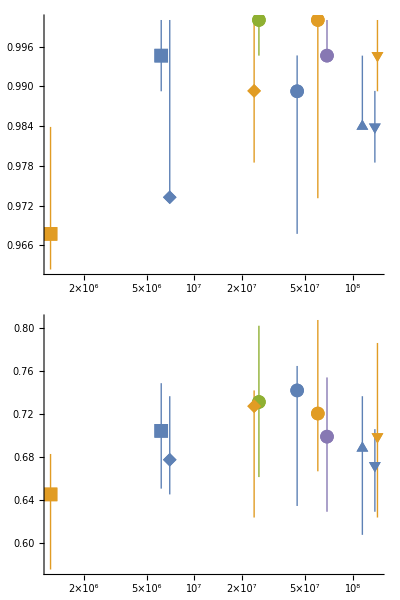

```mathematica
snip[pos_]:=Arrowheads[{{Automatic,pos,Graphics[{BezierCurve[{{0,-(1/2)},{1/2,0},{-(1/2),0},{0,1/2}}]}]}}];
getMaxPadding[p_List]:=Map[Max,(BorderDimensions@Image[Show[#,LabelStyle->White,Background->White]]&/@p)~Flatten~{{3},{2}},{2}]+1
plots5Class=Show[ListPlot[
List/@KeyValueMap[{nParamAssoc[#1],#2}&,KeyTake[accuracies5ClassAssoc,#1]],
PlotStyle->#3,PlotMarkers->Style[#4,14],
ScalingFunctions->{"Log",None},GridLines->{Full,Automatic},GridLinesStyle->Lighter@LightGray
]&@@@({groupedNets,netTypes,colors,pointShapes}ᵀ),PlotRange->All,Joined->True,Mesh->Full,PlotStyle->Red,AxesStyle->{None,snip[1]},PlotRangePadding->None,ImagePadding->30,AspectRatio->{1.1,1}];
plots2Class=Show[ListPlot[
List/@KeyValueMap[{nParamAssoc[#1],#2}&,KeyTake[accuracies2ClassAssoc,#1]],
PlotStyle->#3,PlotMarkers->Style[#4,14],
ScalingFunctions->{"Log",None},GridLines->{Full,Automatic},GridLinesStyle->Lighter@LightGray
]&@@@({groupedNets,netTypes,colors,pointShapes}ᵀ),
PlotRange->All,Joined->True,Mesh->Full,PlotStyle->Blue,Axes->{False,True},AxesStyle->{None,snip[0]},PlotRangePadding->None,ImagePadding->30,AspectRatio->{1.1,1}];

Column[{plots2Class,plots5Class}/. Graphics[x__]:>Graphics[x,ImagePadding->getMaxPadding[{p1,p2}],ImageSize->400]]
```

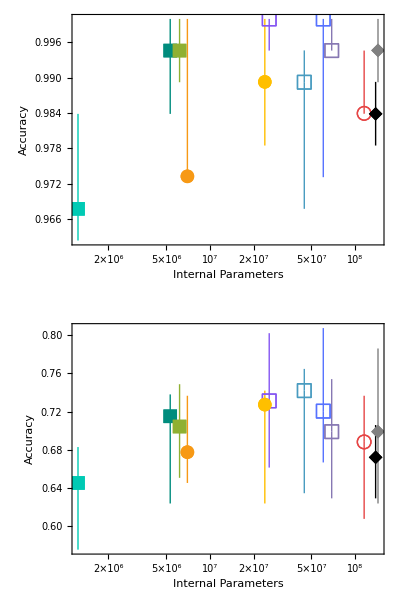

```mathematica
GraphicsColumn[{
Show[plots2Class,
ScalingFunctions->"Log",PlotRange->Full,AspectRatio->1/GoldenRatio,
Frame->True,FrameLabel->{{"Accuracy",None},{"Internal Parameters","2-Class Problem"}},
PlotRange->{0.55,1},
Axes->False],
Show[plots5Class,
ScalingFunctions->"Log",PlotRange->Full,AspectRatio->1/GoldenRatio,
Frame->True,FrameLabel->{{"Accuracy",None},{"Internal Parameters","5-Class Problem"}},
PlotRange->{0.55,1},
Axes->False]
}]
```

```mathematica
GoldenRatio//N
```

1.61803

## Random Weights

```mathematica
rwDir="C:\\Users\\Clint\\Google Drive\\- Programming\\Mathematica\\Machine Learing\\Final Project Hamed\\RNR4061\\Clint\\TransferLearning\\FinalResults\\RandomWeights";
class2Assoc=AssociationThread[First@#->Transpose@Rest@#]&@Import[FileNameJoin[{rwDir,"2C_RandomWeightsResults.csv"}],"CSV"];
accuracies2ClassAssoc=Association[With[{
model=StringReplace[#1,{"RN"->"ResNet","W-"->"Wide ","SqueezeNet"->"SqueezeNet V1.1","SaE-Net"->"Squeeze-and-Excitation Net"," v"->" V","MobileNet"->"MobileNet V2"}],
scoreList=ToExpression@StringReplace[#2,{"["->"{","]"->"}"}]
},
If[Not[scoreList===Null],{model,"ImageNet"}->Around[Median[#],{Median[#]-Min[#],Max[#]-Median[#]}]&@scoreList]
]&@@@({class2Assoc["Model"],class2Assoc["all_test_accuracy"]}ᵀ)/.Null->Sequence[]]

class5Assoc=AssociationThread[First@#->Transpose@Rest@#]&@Import[FileNameJoin[{rwDir,"5C_RandomWeightResults.csv"}],"CSV"];
accuracies5ClassAssoc=Association[With[{
model=StringReplace[#1,{"RN"->"ResNet","W-"->"Wide ","SqueezeNet"->"SqueezeNet V1.1","SaE-Net"->"Squeeze-and-Excitation Net"," v"->" V","MobileNet"->"MobileNet V2"}],
scoreList=ToExpression@StringReplace[#2,{"["->"{","]"->"}"}]
},
If[Not[scoreList===Null],{model,"ImageNet"}->Around[Median[#],{Median[#]-Min[#],Max[#]-Median[#]}]&@scoreList]
]&@@@({class5Assoc["Model"],class5Assoc["all_test_accuracy"]}ᵀ)/.Null->Sequence[]]
```

<|{EfficientNet,ImageNet}→1.,{Inception V3,ImageNet}→1.0.0110.,{MobileNet V2,ImageNet}→1.0.0050.,{ResNet-50,ImageNet}→0.9840.080.016,{SqueezeNet V1.1,ImageNet}→0.9516130.0.04,{ResNet-101,ImageNet}→0.9950.0220.005|>

<|{EfficientNet,ImageNet}→0.6770.0220.022,{Inception V3,ImageNet}→0.7040.060.022,{MobileNet V2,ImageNet}→0.690.040.04,{ResNet-50,ImageNet}→0.6880.0320.06,{SqueezeNet V1.1,ImageNet}→0.6990.060.027,{ResNet-101,ImageNet}→0.7040.0160.027|>

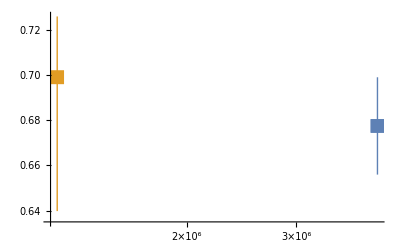
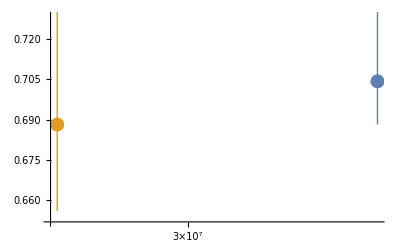
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plots5Class
```

```mathematica
Position
```

Position

```mathematica
(Position[#,Around][[;;,1]]&@Lookup[accuracies5ClassAssoc,#1])&@@@({groupedNets,netTypes,colors,pointShapes}ᵀ)
```

{{1,2,3},{1,3},{2},{},{}}

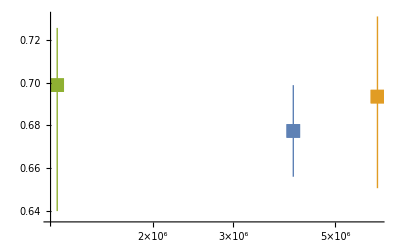
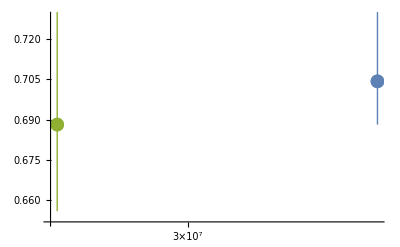
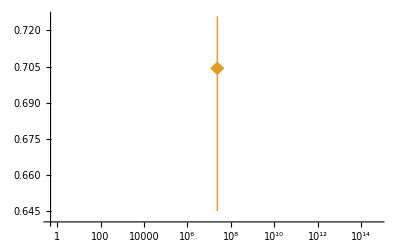
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
With[{idx=Position[#,Around][[;;,1]]&@Lookup[accuracies5ClassAssoc,#1]},
ListPlot[
List/@KeyValueMap[{nParamAssoc[#1],#2}&,KeyTake[accuracies5ClassAssoc,#1[[idx]]]],
PlotStyle->#3[[idx]],PlotMarkers->Style[#4,14],
ScalingFunctions->{"Log",None}(*,GridLines->{Full,Automatic},GridLinesStyle->Lighter@LightGray*)
]
]&@@@({groupedNets,netTypes,colors,pointShapes}ᵀ)
```

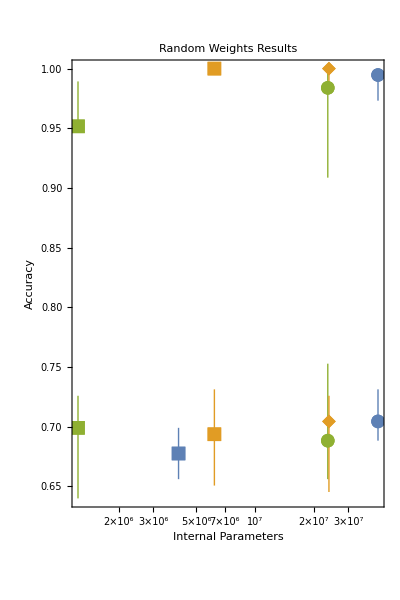

```mathematica
resultsDir=FileNameJoin[{NotebookDirectory[],"FinalResults\\NoInternalUpdatingModelComparison"}];
fnames=FileNames["*mx",resultsDir];

groupedNets={{"SqueezeNet V1.1","EfficientNet","MobileNet V2"},{(*"Ademxapp Model A",*)"ResNet-101","ResNet-152","ResNet-50","Wide ResNet-50-2"},{"Inception V1","Inception V3"},{"Squeeze-and-Excitation Net"},{"VGG-16","VGG-19"}};
groupedNets=Sort/@groupedNets;
groupedNets=Map[{#,"ImageNet"}&,groupedNets,{-1}];

netTypes={"Minimal","Residual","GoogLeNet","SENet","VGG"};

pointShapes={"■","●","◆","▲","▼"};
pointShapes=pointShapes[[;;Length@groupedNets]];

colors={{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885]},{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.528488, 0.470624, 0.701351]},{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051]},{RGBColor[0.368417, 0.506779, 0.709798]},{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051]}};

plots5Class=With[{idx=Position[#,Around][[;;,1]]&@Lookup[accuracies5ClassAssoc,#1]},
ListPlot[
List/@KeyValueMap[{nParamAssoc[#1],#2}&,KeyTake[accuracies5ClassAssoc,#1[[idx]]]],
PlotStyle->#3[[idx]],PlotMarkers->Style[#4,14],
ScalingFunctions->{"Log",None}(*,GridLines->{Full,Automatic},GridLinesStyle->Lighter@LightGray*)
]
]&@@@({groupedNets,netTypes,colors,pointShapes}ᵀ);

plots2Class=With[{idx=Position[#,Around][[;;,1]]&@Lookup[accuracies2ClassAssoc,#1]},
ListPlot[
List/@KeyValueMap[{nParamAssoc[#1],#2}&,KeyTake[accuracies2ClassAssoc,#1[[idx]]]],
PlotStyle->#3[[idx]],PlotMarkers->Style[#4,14],
ScalingFunctions->{"Log",None}(*,GridLines->{Full,Automatic},GridLinesStyle->Lighter@LightGray*)
]
]&@@@({groupedNets,netTypes,colors,pointShapes}ᵀ);

sty=Directive[Black,12];frmStyle=Directive[Black,12];

plt=Show[plots5Class~Join~plots2Class,
ScalingFunctions->"Log",PlotRange->Full,AspectRatio->1.5,
Frame->True,FrameLabel->{{Style["Accuracy",frmStyle],None},{"Internal Parameters",None}},PlotLabel->"Random Weights Results",
FrameStyle->sty,LabelStyle->sty,
PlotRange->{0.55,1},
Axes->False]
```

```mathematica
Clear[compressYAxis];
compressYAxis[plot_,range1_,range2_]:=Module[{ytick1,ytick2,target},
ytick1=FindDivisions[range1,5]/. y_?NumericQ:>{y,y}/. {y_?NumericQ,_}/;y>=range1[[2]]:>Sequence[];
ytick2=FindDivisions[range2,5]/. y_?NumericQ:>{y-range2[[1]]+range1[[2]],y}/. {y_?NumericQ,_}/;y<=range1[[2]]:>Sequence[];
(*epilog=Options[plot,Epilog][[1,2]];*)
target=Subtract@@Reverse@range1/(Subtract@@Reverse@range1+Subtract@@Reverse@range2);
Show[
plot/.{x_?NumericQ,y_?NumericQ/;y>range2[[1]]}:>{x,y-range2[[1]]+range1[[2]]},
FrameTicks->{Automatic,N@SetPrecision[#,2]&/@Join[ytick1,ytick2]},
PlotRange->{range1[[1]],range1[[2]]+Subtract@@Reverse@range2},
Epilog->Join[epilog,{
White,Rectangle[Scaled[{-0.1,0.98 target}],Scaled[{1.1,1.02 target}]],
Black,Text["~",Scaled[{-.01,.984target}],{-1.5,0}],Text["~",Scaled[{-.01,1.02 target}],{-1.5,0}](*,
Black,Text[Rotate["\\",π/2],Scaled[{.975,.984target}],{-1.5,0}],Text[Rotate["\\",π/2],Scaled[{.975,1.02 target}],{-1.5,0}]*)
}
]]]
compressYAxis[plt,{0.58,0.76},{0.89,1}]
plt
```

-Graphics-

## Score Scatter

```mathematica
resultsDir=FileNameJoin[{NotebookDirectory[],"FinalResults\\NoInternalUpdatingModelComparison"}];
fnames=FileNames["*mx",resultsDir];
```

```mathematica
fnames2Class=Rest@Select[fnames,StringContainsQ["2Class"]];

netkeys=Flatten[
StringCases[fnames2Class,"Class - "~~m___~~" - "~~ds___~~"Pretrain.mx":>{m,ds}],
{2}][[1]]/."ImageNet Competition Data"->"ImageNet";


accuracies=Table[
results=AssociationTranspose@Import[fname];
Around[Median[#],{Median[#]-Min[#],Max[#]-Median[#]}]&@(Max/@(#["Accuracy"]&/@results["ValidationMeasurementsLists"]))
(*accs=#["Accuracy"]⟦results["BestValidationRound"]⟧&/@results["ValidationMeasurementsLists"]*)
,{fname,fnames2Class}];
accuraciesAssoc=AssociationThread[netkeys->accuracies];
```

```mathematica
accuraciesAssoc
```

<|{EfficientNet,ImageNet}→0.9950.0110.005,{Inception V1,ImageNet}→0.973260.000140.027,{Inception V3,ImageNet}→0.9890.0110.011,{MobileNet V2,ImageNet}→0.9950.0050.005,{ResNet-101,ImageNet}→0.9890.0220.005,{ResNet-152,ImageNet}→1.0.0270.,{ResNet-50,ImageNet}→1.0.0050.,{Squeeze-and-Excitation Net,ImageNet}→0.983960.000090.011,{SqueezeNet V1.1,ImageNet}→0.9680.0050.016,{VGG-16,ImageNet}→0.9840.0050.005,{VGG-19,ImageNet}→0.9950.0050.005,{Wide ResNet-50-2,ImageNet}→0.9946240.0.005|>

```mathematica
nParamAssoc
```

<|{Ademxapp Model A,ImageNet}→109215656,{EfficientNet,ImageNet with AdvProp and AutoAugment}→5330564,{EfficientNet,ImageNet with NoisyStudent}→5330564,{EfficientNet,ImageNet}→5330564,{Inception V1,ImageNet}→6998552,{Inception V3,ImageNet}→23885392,{MobileNet V2,ImageNet}→6182473,{ResNet-101,ImageNet}→44654504,{ResNet-152,ImageNet}→60344232,{ResNet-50,ImageNet}→25610216,{Squeeze-and-Excitation Net,ImageNet}→115336536,{SqueezeNet V1.1,ImageNet}→1235496,{VGG-16,ImageNet}→138357544,{VGG-19,ImageNet}→143667240,{Wide ResNet-50-2,ImageNet}→68951464|>

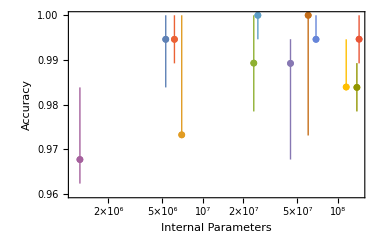

```mathematica
plotDat=KeyValueMap[{nParamAssoc[#1],#2}&,accuraciesAssoc];
SwatchLegend[ColorData[97]/@Range@Length@#,First/@#]&@Keys@accuraciesAssoc
plt2=ListPlot[List/@plotDat,
ScalingFunctions->{"Log",None},PlotRange->{Automatic,{0.96,1}},
Frame->True,FrameLabel->{{"Accuracy",None},{"Internal Parameters","2-Class Problem"}}
]
```

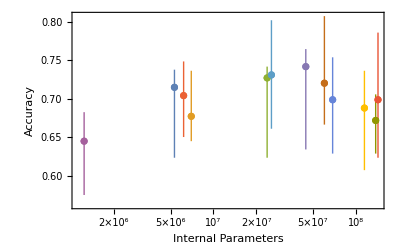

```mathematica
fnames5Class=Rest@Select[fnames,StringContainsQ["5Class"]];

netkeys=Flatten[
StringCases[fnames5Class,"Class - "~~m___~~" - "~~ds___~~"Pretrain.mx":>{m,ds}],
{2}][[1]]/."ImageNet Competition Data"->"ImageNet";


accuracies=Table[
results=AssociationTranspose@Import[fname];
Around[Median[#],{Median[#]-Min[#],Max[#]-Median[#]}]&@(Max/@(#["Accuracy"]&/@results["ValidationMeasurementsLists"]))
(*accs=#["Accuracy"]⟦results["BestValidationRound"]⟧&/@results["ValidationMeasurementsLists"]*)
,{fname,fnames2Class}];
accuraciesAssoc=AssociationThread[netkeys->accuracies];

plotDat=KeyValueMap[{nParamAssoc[#1],#2}&,accuraciesAssoc];
plt5=ListPlot[List/@plotDat,
ScalingFunctions->{"Log",None},PlotRange->{Automatic,Automatic},
Frame->True,FrameLabel->{{"Accuracy",None},{"Internal Parameters","5-Class Problem"}}
]
```

```mathematica
AssociationTranspose[assoc_]:=Normal@Transpose@Dataset[assoc]
```

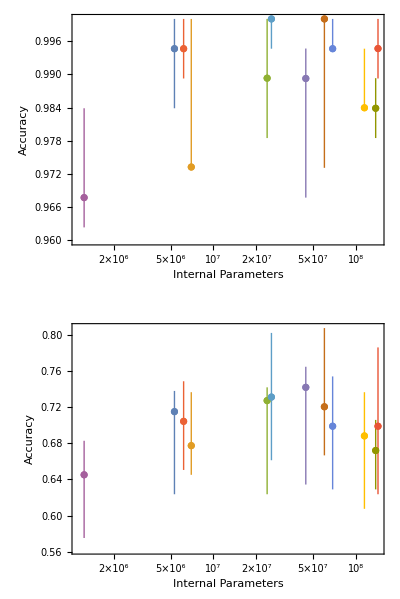

```mathematica
GraphicsColumn[{plt2,plt5}]
```

## Test Set Sizes

```mathematica
resultsDir=FileNameJoin[{NotebookDirectory[],"FinalResults\\TrainSizeComparison"}];
fnames=FileNames["*mx",resultsDir];
fnames=Select[fnames,StringContainsQ["ResNet-50"]];
```

```mathematica
netkeys=Flatten[
StringCases[fnames," - "~~n_~~"Class - "~~m___~~" Training Imgs - "~~mdl___~~" - "~~ds___~~".mx":>{ToExpression@n,ToExpression@m,mdl,ds}],
{2}][[1]]/."ImageNet Competition Data"->"ImageNet";
fileAssoc=AssociationThread[netkeys->fnames];
```

```mathematica
accuracies=(
results=AssociationTranspose@Import[#];
(*Around[Quantile[#,1/2],{Quantile[#,1/2]-Quantile[#,1/4],Quantile[#,3/4]-Quantile[#,1/2]}]&@(Max/@(#["Accuracy"]&/@results["ValidationMeasurementsLists"]))*)
Around[Median[#],{Median[#]-Min[#],Max[#]-Median[#]}]&[Max/@(#["Accuracy"]&/@results["ValidationMeasurementsLists"])]
(*Around[Mean[#],StandardDeviation[#]]&[Max/@(#["Accuracy"]&/@results["ValidationMeasurementsLists"])]*)
)&/@fileAssoc;
```

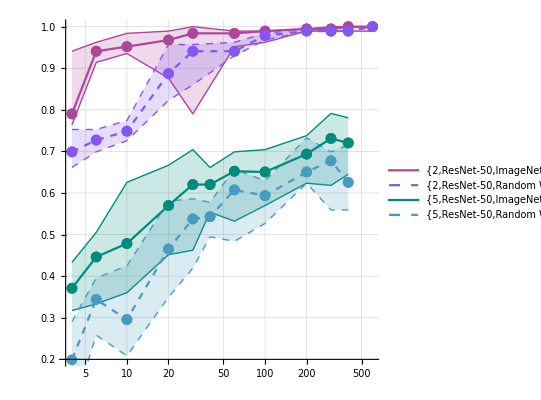

```mathematica
SortBy[({#[[2]],accuracies[#]}&/@#),First]&/@GroupBy[netkeys,#[[{1,3,4}]]&];
ListLinePlot[%,IntervalMarkers->"Bands",ScalingFunctions->{"Log",None},GridLines->{Full,Automatic},GridLinesStyle->LightGray,AspectRatio->1,PlotRange->{0.2,1},Mesh->Full,PlotStyle->{RGBColor[0.68343, 0.28, 0.602415],Directive[{RGBColor[0.519913, 0.338384, 0.950217],Dashed}],RGBColor[0., 0.547860708344002, 0.48916937319711223],Directive[{RGBColor[0.28240003484173815, 0.6090799721266095, 0.7538800418100857],Dashed}]}]
```

```mathematica
LineLegend[{RGBColor[0.68343, 0.28, 0.602415],Directive[{RGBColor[0.519913, 0.338384, 0.950217],Dashed}],RGBColor[0., 0.547860708344002, 0.48916937319711223],Directive[{RGBColor[0.28240003484173815, 0.6090799721266095, 0.7538800418100857],Dashed}]},{"2 Class ImageNet Pretrain","2 Class Random Weights","5 Class ImageNet Pretrain","5 Class Random Weights"}]
```

```mathematica
{RGBColor[0., 0.7904149413567342, 0.7051172293440505],RGBColor[0., 0.547860708344002, 0.48916937319711223],RGBColor[0.560181, 0.691569, 0.194885]},{RGBColor[0.28240003484173815, 0.6090799721266095, 0.7538800418100857],RGBColor[0.337228, 0.447663, 1.],RGBColor[0.519913, 0.338384, 0.950217],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.68343, 0.28, 0.602415]}
```

#### Confusion Matrix Data

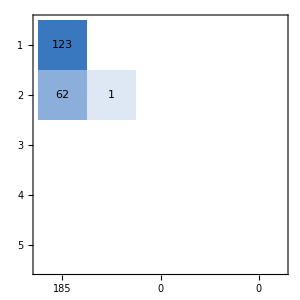
```mathematica
{{"actual class", -Graphics-}, {, "predicted class"}}//FullForm
```

List[List[Rotate["actual class",1.5708],Graphics[Raster[List[List[List[1.,1.,1.],List[1.,1.,1.],List[1.,1.,1.],List[1.,1.,1.],List[1.,1.,1.]],List[List[1.,1.,1.],List[1.,1.,1.],List[1.,1.,1.],List[1.,1.,1.],List[1.,1.,1.]],List[List[1.,1.,1.],List[1.,1.,1.],List[1.,1.,1.],List[1.,1.,1.],List[1.,1.,1.]],List[List[0.546341,0.687707,0.853659],List[0.867683,0.908915,0.957317],List[1.,1.,1.],List[1.,1.,1.],List[1.,1.,1.]],List[List[0.225,0.4665,0.75],List[1.,1.,1.],List[1.,1.,1.],List[1.,1.,1.],List[1.,1.,1.]]],List[List[0,0],List[5,5]],List[0,1]],Rule[Background,GrayLevel[1]],Rule[BaseStyle,Directive[Rule[FontSize,7],Rule[FontFamily,"Verdana"],Rule[FontWeight,"Thin"],Rule[FontTracking,"Condensed"]]],Rule[Epilog,List[List[Inset[123,List[0.5,4.5],ImageScaled[List[Rational[1,2],Rational[1,2]]]]],List[Inset[62,List[0.5,3.5],ImageScaled[List[Rational[1,2],Rational[1,2]]]],Inset[1,List[1.5,3.5],ImageScaled[List[Rational[1,2],Rational[1,2]]]]],List[],List[],List[]]],Rule[Frame,True],Rule[FrameLabel,List[None,None]],Rule[FrameTicks,List[List[List[List[4.5,Rotate[1,0.]],List[3.5,Rotate[2,0.]],List[2.5,Rotate[3,0.]],List[1.5,Rotate[4,0.]],List[0.5,Rotate[5,0.]]],List[List[4.5,123],List[3.5,63],List[2.5,0],List[1.5,0],List[0.5,0]]],List[List[List[0.5,Rotate[185,1.5708]],List[1.5,Rotate[1,1.5708]],List[2.5,Rotate[0,1.5708]],List[3.5,Rotate[0,1.5708]],List[4.5,Rotate[0,1.5708]]],List[List[0.5,Rotate[1,1.5708]],List[1.5,Rotate[2,1.5708]],List[2.5,Rotate[3,1.5708]],List[3.5,Rotate[4,1.5708]],List[4.5,Rotate[5,1.5708]]]]]],Rule[GridLinesStyle,Directive[GrayLevel[0.5,0.4]]],Rule[ImagePadding,List[List[All,24.],List[24.,All]]],Rule[ImageSize,300],Rule[Method,List[Rule["AxisPadding",Scaled[0.02]],Rule["DefaultBoundaryStyle",Automatic],Rule["DefaultGraphicsInteraction",List[Rule["Version",1.2],Rule["TrackMousePosition",List[True,False]],Rule["Effects",List[Rule["Highlight",List[Rule["ratio",2]]],Rule["HighlightPoint",List[Rule["ratio",2]]],Rule["Droplines",List[Rule["freeformCursorMode",True],Rule["placement",List[Rule["x","All"],Rule["y","None"]]]]]]]]],Rule["DefaultPlotStyle",Automatic],Rule["DomainPadding",Scaled[0.02]],Rule["RangePadding",Scaled[0.05]]]]]],List[Null,"predicted class"]]

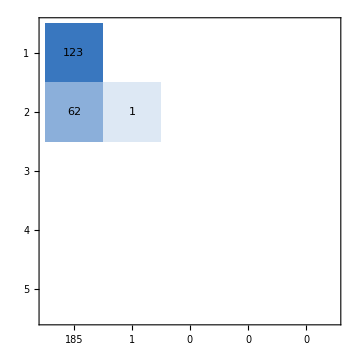
```mathematica
{{"actual class", -Graphics-}, {, "predicted class"}}[[1,2,1,1]]//Reverse
%//Image
Map[%%,Mean,{-1}]
(1-Map[Mean,%%%,{-2}])
```

{{{0.225,0.4665,0.75},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.}},{{0.546341,0.687707,0.853659},{0.867683,0.908915,0.957317},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.}},{{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.}},{{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.}},{{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.}}}

-Graphics-

{{{0.225,0.4665,0.75},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.}},{{0.546341,0.687707,0.853659},{0.867683,0.908915,0.957317},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.}},{{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.}},{{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.}},{{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.}}}[Mean]

{{97.1465,0.,0.,0.,0.},{56.8662,16.586,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.}}

```mathematica
List[List[Inset[123,List[0.5,4.5],ImageScaled[List[Rational[1,2],Rational[1,2]]]]],List[Inset[62,List[0.5,3.5],ImageScaled[List[Rational[1,2],Rational[1,2]]]],Inset[1,List[1.5,3.5],ImageScaled[List[Rational[1,2],Rational[1,2]]]]],List[],List[],List[]]
```

{{Inset[123,{0.5,4.5},ImageScaled[{1/2,1/2}]]},{Inset[62,{0.5,3.5},ImageScaled[{1/2,1/2}]],Inset[1,{1.5,3.5},ImageScaled[{1/2,1/2}]]},{},{},{}}

```mathematica
{{"actual class", -Graphics-}, {, "predicted class"}}[[1,2,4,2]]//Reverse
```

{{},{},{},{Inset[62,{0.5,3.5},ImageScaled[{1/2,1/2}]],Inset[1,{1.5,3.5},ImageScaled[{1/2,1/2}]]},{Inset[123,{0.5,4.5},ImageScaled[{1/2,1/2}]]}}

### Effects of noise

```mathematica
resultsDir=FileNameJoin[{NotebookDirectory[],"FinalResults\\EffectsOfDataAug"}];
fnames=FileNames["*mx",resultsDir];
fnames=Select[fnames,StringContainsQ["ResNet"]];
```

```mathematica
fnames
```

{C:\Users\Clint\Google Drive\- Programming\Mathematica\Machine Learing\Final Project Hamed\RNR4061\Clint\TransferLearning\FinalResults\EffectsOfDataAug\Results 5FoldCV - 2Class - GaussianNoise - 0.1 std - ResNet-152 - ImageNet Pretrain.mx,C:\Users\Clint\Google Drive\- Programming\Mathematica\Machine Learing\Final Project Hamed\RNR4061\Clint\TransferLearning\FinalResults\EffectsOfDataAug\Results 5FoldCV - 2Class - GaussianNoise - 0.2 std - ResNet-152 - ImageNet Pretrain.mx,C:\Users\Clint\Google Drive\- Programming\Mathematica\Machine Learing\Final Project Hamed\RNR4061\Clint\TransferLearning\FinalResults\EffectsOfDataAug\Results 5FoldCV - 2Class - GaussianNoise - 0.4 std - ResNet-152 - ImageNet Pretrain.mx,C:\Users\Clint\Google Drive\- Programming\Mathematica\Machine Learing\Final Project Hamed\RNR4061\Clint\TransferLearning\FinalResults\EffectsOfDataAug\Results 5FoldCV - 2Class - GaussianNoise - 0.6 std - ResNet-152 - ImageNet Pretrain.mx,C:\Users\Clint\Google Drive\- Programming\Mathematica\Machine Learing\Final Project Hamed\RNR4061\Clint\TransferLearning\FinalResults\EffectsOfDataAug\Results 5FoldCV - 2Class - GaussianNoise - 0.8 std - ResNet-152 - ImageNet Pretrain.mx,C:\Users\Clint\Google Drive\- Programming\Mathematica\Machine Learing\Final Project Hamed\RNR4061\Clint\TransferLearning\FinalResults\EffectsOfDataAug\Results 5FoldCV - 2Class - GaussianNoise - 0. std - ResNet-152 - ImageNet Pretrain.mx,C:\Users\Clint\Google Drive\- Programming\Mathematica\Machine Learing\Final Project Hamed\RNR4061\Clint\TransferLearning\FinalResults\EffectsOfDataAug\Results 5FoldCV - 2Class - GaussianNoise - 1. std - ResNet-152 - ImageNet Pretrain.mx,C:\Users\Clint\Google Drive\- Programming\Mathematica\Machine Learing\Final Project Hamed\RNR4061\Clint\TransferLearning\FinalResults\EffectsOfDataAug\Results 5FoldCV - 5Class - GaussianNoise - 0.1 std - ResNet-152 - ImageNet Pretrain.mx,C:\Users\Clint\Google Drive\- Programming\Mathematica\Machine Learing\Final Project Hamed\RNR4061\Clint\TransferLearning\FinalResults\EffectsOfDataAug\Results 5FoldCV - 5Class - GaussianNoise - 0.2 std - ResNet-152 - ImageNet Pretrain.mx,C:\Users\Clint\Google Drive\- Programming\Mathematica\Machine Learing\Final Project Hamed\RNR4061\Clint\TransferLearning\FinalResults\EffectsOfDataAug\Results 5FoldCV - 5Class - GaussianNoise - 0.4 std - ResNet-152 - ImageNet Pretrain.mx,C:\Users\Clint\Google Drive\- Programming\Mathematica\Machine Learing\Final Project Hamed\RNR4061\Clint\TransferLearning\FinalResults\EffectsOfDataAug\Results 5FoldCV - 5Class - GaussianNoise - 0.6 std - ResNet-152 - ImageNet Pretrain.mx,C:\Users\Clint\Google Drive\- Programming\Mathematica\Machine Learing\Final Project Hamed\RNR4061\Clint\TransferLearning\FinalResults\EffectsOfDataAug\Results 5FoldCV - 5Class - GaussianNoise - 0.8 std - ResNet-152 - ImageNet Pretrain.mx,C:\Users\Clint\Google Drive\- Programming\Mathematica\Machine Learing\Final Project Hamed\RNR4061\Clint\TransferLearning\FinalResults\EffectsOfDataAug\Results 5FoldCV - 5Class - GaussianNoise - 0. std - ResNet-152 - ImageNet Pretrain.mx,C:\Users\Clint\Google Drive\- Programming\Mathematica\Machine Learing\Final Project Hamed\RNR4061\Clint\TransferLearning\FinalResults\EffectsOfDataAug\Results 5FoldCV - 5Class - GaussianNoise - 1. std - ResNet-152 - ImageNet Pretrain.mx}

```mathematica
netkeys=Flatten[
StringCases[fnames," - "~~n_~~"Class - GaussianNoise - "~~std___~~" std - "~~mdl___~~" - "~~ds___~~".mx":>{ToExpression@n,ToExpression@std,mdl,ds}],
{2}][[1]]/."ImageNet Competition Data"->"ImageNet";
fileAssoc=AssociationThread[netkeys->fnames];
```

```mathematica
accuracies=(
results=Import[#];
Around[Median[#],{Median[#]-Min[#],Max[#]-Median[#]}]&[Max[#["ValidationMeasurementsLists"]["Accuracy"]]&/@results]
)&/@fileAssoc
```

<|{2,0.1,ResNet-152,ImageNet Pretrain}→1.0.0160.,{2,0.2,ResNet-152,ImageNet Pretrain}→1.0.0160.,{2,0.4,ResNet-152,ImageNet Pretrain}→1.0.0160.,{2,0.6,ResNet-152,ImageNet Pretrain}→1.0.0160.,{2,0.8,ResNet-152,ImageNet Pretrain}→1.0.0160.,{2,0.,ResNet-152,ImageNet Pretrain}→1.0.0160.,{5,0.1,ResNet-152,ImageNet Pretrain}→0.710.060.09,{5,0.2,ResNet-152,ImageNet Pretrain}→0.710.060.09,{5,0.4,ResNet-152,ImageNet Pretrain}→0.710.060.09,{5,0.6,ResNet-152,ImageNet Pretrain}→0.710.060.09,{5,0.8,ResNet-152,ImageNet Pretrain}→0.710.060.09,{5,0.,ResNet-152,ImageNet Pretrain}→0.710.060.09,{5,1.,ResNet-152,ImageNet Pretrain}→0.710.060.09|>

## Weighting

```mathematica
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/MathematicaForPredictionUtilities.m"]
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/ROCFunctions.m"]
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/ClassifierEnsembles.m"]
```

Importing from GitHub:  MosaicPlot.m

Importing from GitHub:  CrossTabulate.m

Importing from GitHub:  ParetoPrincipleAdherence.m

```mathematica
Clear[ROCAssociationQ];
ROCAssociationQ[ obj_ ] :=
    AssociationQ[obj] &&
        Length[Intersection[Keys[obj], {"TruePositive", "FalsePositive", "TrueNegative", "FalseNegative"}]] == 4;

TPR[rocAssoc_?ROCAssociationQ] := (rocAssoc["TruePositive"]) / (rocAssoc["TruePositive"] + rocAssoc["FalseNegative"]);
TPR[rocs : ({_?ROCAssociationQ..} | <|_?ROCAssociationQ..|> )] := Map[TPR, rocs];
SPC[rocAssoc_?ROCAssociationQ] := (rocAssoc["TrueNegative"]) / (rocAssoc["FalsePositive"] + rocAssoc["TrueNegative"]);
SPC[rocs : ({_?ROCAssociationQ..} | <|_?ROCAssociationQ..|> )] := Map[SPC, rocs];
PPV[rocAssoc_?ROCAssociationQ] := (rocAssoc["TruePositive"]) / (rocAssoc["TruePositive"] + rocAssoc["FalsePositive"]);
PPV[rocs : ({_?ROCAssociationQ..} | <|_?ROCAssociationQ..|> )] := Map[PPV, rocs];
NPV[rocAssoc_?ROCAssociationQ] := (rocAssoc["TrueNegative"]) / (rocAssoc["TrueNegative"] + rocAssoc["FalseNegative"]);
NPV[rocs : ({_?ROCAssociationQ..} | <|_?ROCAssociationQ..|> )] := Map[NPV, rocs];
FPR[rocAssoc_?ROCAssociationQ] := (rocAssoc["FalsePositive"]) / (rocAssoc["FalsePositive"] + rocAssoc["TrueNegative"]);
FPR[rocs : ({_?ROCAssociationQ..} | <|_?ROCAssociationQ..|> )] := Map[FPR, rocs];
FDR[rocAssoc_?ROCAssociationQ] := (rocAssoc["FalsePositive"]) / (rocAssoc["FalsePositive"] + rocAssoc["TruePositive"]);
FDR[rocs : ({_?ROCAssociationQ..} | <|_?ROCAssociationQ..|> )] := Map[FDR, rocs];
FNR[rocAssoc_?ROCAssociationQ] := (rocAssoc["FalseNegative"]) / (rocAssoc["FalseNegative"] + rocAssoc["TruePositive"]);
FNR[rocs : ({_?ROCAssociationQ..} | <|_?ROCAssociationQ..|> )] := Map[FNR, rocs];
ACC[rocAssoc_?ROCAssociationQ] := (rocAssoc["TruePositive"] + rocAssoc["TrueNegative"]) / Total[Values[rocAssoc]];
ACC[rocs : ({_?ROCAssociationQ..} | <|_?ROCAssociationQ..|> )] := Map[ACC, rocs];
FOR[rocAssoc_?ROCAssociationQ] := 1 - NPV[rocAssoc];
FOR[rocs : ({_?ROCAssociationQ..} | <|_?ROCAssociationQ..|> )] := Map[FOR, rocs];
F1[rocAssoc_?ROCAssociationQ] := 2 * PPV[rocAssoc] * TPR[rocAssoc] / ( PPV[rocAssoc] + TPR[rocAssoc] );
F1[rocs : ({_?ROCAssociationQ..} | <|_?ROCAssociationQ..|> )] := Map[F1, rocs];
```

```mathematica
resultsDir=FileNameJoin[{NotebookDirectory[],"FinalResults\\WeightingEffects"}];
fnames=FileNames["*mx",resultsDir];
fnames=Select[fnames,StringContainsQ["2Class"]];
```

```mathematica
netkeys=Flatten[
StringCases[fnames," - "~~n_~~"Class - "~~type___~~" - "~~mdl___~~".mx":>{ToExpression@n,type,mdl}],
{2}][[1]]/."ImageNet Competition Data"->"ImageNet";
fileAssoc=AssociationThread[netkeys->fnames];
```

```mathematica
accuracies=(
results=AssociationTranspose@Import[#]//N;
{
results["rocRange"][[1]],
results["ROCs"],
(* actuals may be opposite if 1 is + and 2 is - *)
Around[Mean[#],StandardDeviation[#]]&/@Transpose[FNR/@results["ROCs"]],
Around[Mean[#],StandardDeviation[#]]&/@Transpose[FPR/@results["ROCs"]],
Around[Mean[#],StandardDeviation[#]]&/@Transpose[ACC/@results["ROCs"]]
}
)&/@fileAssoc;
accuracies=KeySelect[accuracies,Not@StringContainsQ[#[[2]],("None"|"1e4")]&];
```

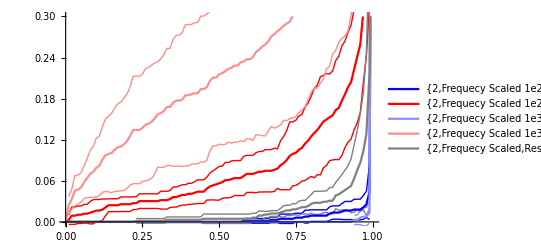

```mathematica
ListLinePlot[Transpose/@accuracies[[;;,{1,3}]],PlotRange->{0,.3},IntervalMarkers->"Bands",PlotStyle->(Directive[{#,Thick}]&/@{Blue,Red,Lighter@Lighter@Blue,Lighter@Lighter@Red,Gray})]
```

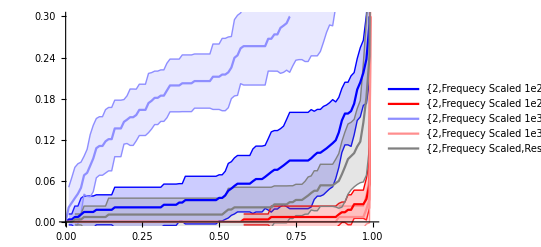

```mathematica
ListLinePlot[Transpose/@accuracies[[;;,{1,4}]],PlotRange->{0,.3},IntervalMarkers->"Bands",PlotStyle->(Directive[{#,Thick}]&/@{Blue,Red,Lighter@Lighter@Blue,Lighter@Lighter@Red,Gray})]
```

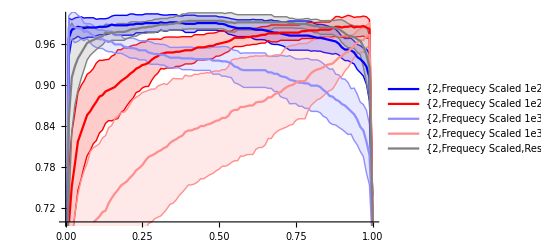

```mathematica
ListLinePlot[Transpose/@accuracies[[;;,{1,5}]],IntervalMarkers->"Bands",PlotRange->{.7,1},PlotStyle->(Directive[{#,Thick(*,Dashed*)}]&/@{Blue,Red,Lighter@Lighter@Blue,Lighter@Lighter@Red,Gray})]
```

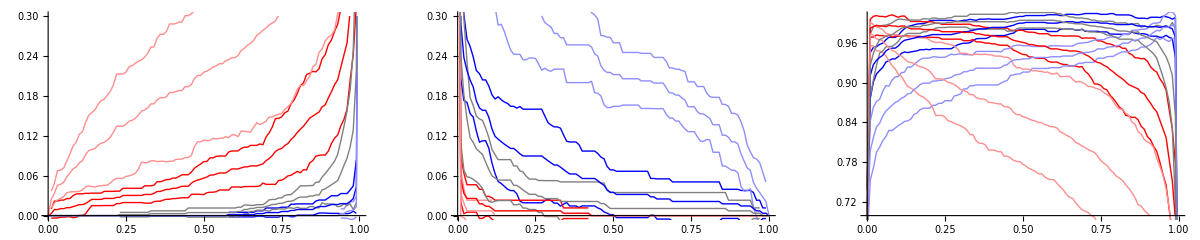

```mathematica
ip={{20,10},{Automatic,Automatic}};
plotOpts={IntervalMarkers->"Bands",PlotStyle->(Directive[{#,Thick}]&/@{Blue,Red,Lighter@Lighter@Blue,Lighter@Lighter@Red,Gray}),ImagePadding->ip,PlotLegends->None};
FNRPlot=ListLinePlot[Transpose/@accuracies[[;;,{1,3}]],PlotRange->{0,.3},Sequence@@plotOpts];
FPRPlot=ListLinePlot[Transpose/@accuracies[[;;,{1,4}]],PlotRange->{0,.3},Sequence@@plotOpts];
ACCPlot=ListLinePlot[Transpose/@accuracies[[;;,{1,5}]],PlotRange->{.7,1},Sequence@@plotOpts];
GraphicsRow[{FNRPlot,FPRPlot,ACCPlot}]
```

```mathematica
Exit[]
```

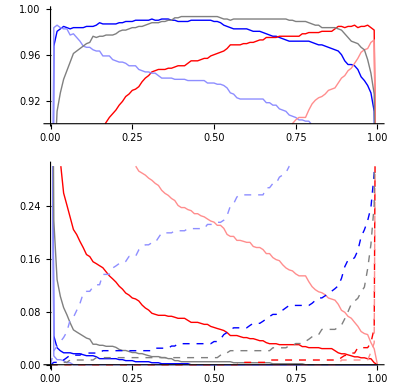

```mathematica
ip={{30,10},{Automatic,Automatic}};
plotOpts={IntervalMarkers->"None",ImagePadding->ip,PlotLegends->None};
FNRPlot=ListLinePlot[Transpose/@accuracies[[;;,{1,3}]],PlotRange->{0,.3},Sequence@@plotOpts,PlotStyle->(Directive[{#,Thick}]&/@{Blue,Red,Lighter@Lighter@Blue,Lighter@Lighter@Red,Gray})];
FPRPlot=ListLinePlot[Transpose/@accuracies[[;;,{1,4}]],PlotRange->{0,.3},Sequence@@plotOpts,PlotStyle->(Directive[{#,Thick,Dashed}]&/@{Blue,Red,Lighter@Lighter@Blue,Lighter@Lighter@Red,Gray})];
ACCPlot=ListLinePlot[Transpose/@accuracies[[;;,{1,5}]],PlotRange->{.9,1},Sequence@@plotOpts,PlotStyle->(Directive[{#,Thick}]&/@{Blue,Red,Lighter@Lighter@Blue,Lighter@Lighter@Red,Gray}),AspectRatio->1/3];
GraphicsColumn[{ACCPlot,Show[{FNRPlot,FPRPlot}]}]
```

```mathematica
LineLegend[(Directive[{#,Thick}]&/@{Blue,Lighter@Lighter@Blue,Red,Lighter@Lighter@Red,Gray}),{"1e2 Negative Weighting","1e3 Negative Weighting","1e2 Positive Weighting","1e3 Positive Weighting","Frequency Weighting"},LegendLayout->"Row",ImageSize->{800,40}]
```

## General Figures

```mathematica
ds=Import@FileNameJoin[{ParentDirectory@NotebookDirectory[],"BigImageDataCorrected_Novelo.mx"}];
```

```mathematica
cnts=Counts@Normal@ds[Select[#class≤5&]][All,"class"]
```

<|2→166,3→148,4→90,5→190,1→337|>

```mathematica
First@Keys@ds
```

```mathematica
exts={"bmp","tif","bmp","tif","tif"}
GraphicsGrid[Transpose@Table[
choice=RandomChoice[Normal@ds[Select[#class==n&&StringEndsQ[#name,exts[[n]]]&]]];
Echo@choice["nameFull"];
{
choice["img"],choice["imgCorrected"]
},
{n,1,5}]]
```

{bmp,tif,bmp,tif,tif}

1 (323 images)\Nov 5, 2008 (89 images)\42-1.bmp

2 (160 images)\Mar 25, 2010 (25 images)\596.tif

3 (146 images)\Mar 13, 2009 (55 images)\432-3.bmp

4 (90 images)\PondG1G2 2010 (7 images)\3494A.tif

5 (190 images)\PondB9 2010 (14 images)\629_5.tif

-Graphics-

```mathematica
choice["nameFull"]
```

5 (190 images)\PondB9 2010 (14 images)\652_5.tif

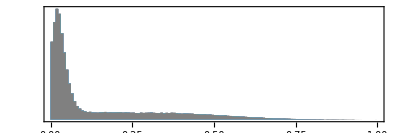

```mathematica
ImageHistogram[choice["img"]][[1;;2]]
```

```mathematica
RandomChoice[Normal@ds[Select[#class==1&&StringEndsQ[#name,"bmp"]&]]]
```

<|name→5-1.bmp,nameFull→1 (323 images)\Nov 5, 2008 (89 images)\5-1.bmp,class→1,pond→Missing[],imgRaw→-Graphics-,date→Wed 5 Nov 2008,depth→80 mm,freq→8.0 MHz,img→-Graphics-,imgCropped→-Graphics-,imgCorrected→-Graphics-|>

```mathematica
-Graphics-//ImageDimensions
```

{407,200}

```mathematica
ds[Select[#class==1&&StringEndsQ[#name,"bmp"]&]]
```

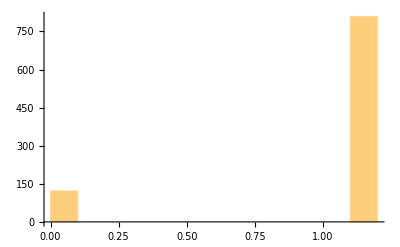

```mathematica
Histogram[ImageDistance[ImageTake[#imgRaw,{-1,-1},{-1,-1}],-Graphics-]&/@Normal@ds[Select[#class<=5&]],{0.1}]
```

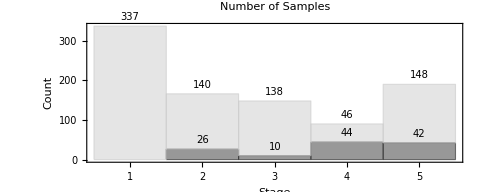

```mathematica
d1Classes=Normal@ds[Select[#class<=5&&(ImageDistance[ImageTake[#imgRaw,{-1,-1},{-1,-1}],-Graphics-]>=0.5)&]][All,"class"];
d2Classes=Normal@ds[Select[#class<=5&&(ImageDistance[ImageTake[#imgRaw,{-1,-1},{-1,-1}],-Graphics-]<=0.5)&]][All,"class"];
sty=Directive[Black,10];
Histogram[{d2Classes,d1Classes},ChartLayout->"Stacked",LabelingFunction->Above,
PlotTheme->"Monochrome",Frame->{{True,False},{True,False}},PlotLabel->"Number of Samples",FrameLabel->{"Stage","Count"},FrameStyle->sty,LabelStyle->sty,AspectRatio->1/2.5]
```

```mathematica
ColorData[105]/@{2,3}
```

{RGBColor[0.680612, 0.714512, 0.],RGBColor[0.0173758, 0.686099, 0.720851]}

```mathematica
Length@Normal@ds[Select[#class<=5&]]
Length/@{d2Classes,d1Classes}
```

931

{122,809}